# Scattering by the homogeneous sphere (Mie scattering)

```mathematica
(* See H M Nussenzveig, Diffraction effects in semiclassical scattering *)
(* N = diffractive index = 4/3 for water *)
Clear[n,α,β,l];
RicBes[l_,z_]:=z*SphericalBesselJ[l,z];
RicHank1[l_,z_]:= z*SphericalHankelH1[l,z];
RicHank2[l_,z_]:= z*SphericalHankelH2[l,z];
phaseAnumer=-RicHank2[l,β];
phaseAdenom=RicHank1[l,β];
phaseA=phaseAnumer/phaseAdenom;
ee1=1;
ee2=1/n^2;
phaseB1numer=((D[RicHank2[l,β],β]/RicHank2[l,β])-n*ee1*(D[RicBes[l,α],α]/RicBes[l,α]));
phaseB1denom=((D[RicHank1[l,β],β]/RicHank1[l,β])-n*ee1*(D[RicBes[l,α],α]/RicBes[l,α]));
phaseB1=phaseB1numer/phaseB1denom;
phaseB2numer=((D[RicHank2[l,β],β]/RicHank2[l,β])-n*ee2*(D[RicBes[l,α],α]/RicBes[l,α]));
phaseB2denom=((D[RicHank1[l,β],β]/RicHank1[l,β])-n*ee2*(D[RicBes[l,α],α]/RicBes[l,α]));
phaseB2=phaseB2numer/phaseB2denom;
SS1=phaseA*phaseB1;
SS2=phaseA*phaseB2;
```

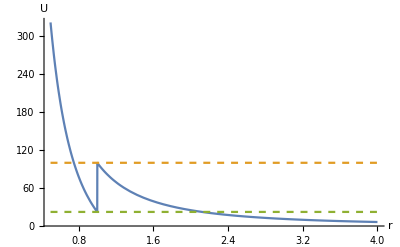

```mathematica
(* Sketch the effective potential *)
Ueff=λ^2/r^2-(n^2-1)*ω^2*HeavisideTheta[R-r];
n0=4/3;
mysubs={λ-> 10,ω->10,R->1,n->4/3};
Plot[{Ueff/.mysubs,(λ/R)^2/.mysubs,(λ/R)^2-(n^2-1)*ω^2/.mysubs},{r,0.5,4},PlotRange->All,PlotStyle->{Solid,Dashed,Dashed},AxesLabel->{r,U}]
```

```mathematica
Ueff/.{λ-> 10,ω->10,R->1}
```

100/r^2-100 (-1+n^2) HeavisideTheta[1-r]

```mathematica
βmax=20;
fn=SS1/.{α-> β*n}/.{β->βmax,n->4/3,l-> λ-1/2};
Plot3D[Log[Abs[fn/.{λ->λre+I*λim}]],{λre,1,1.5*βmax},{λim,0.0,βmax},PlotPoints->40]
```

-Graphics3D-

{λ→22.9491+0.08941 ⅈ}

2.36896×10^11+1.00063×10^12 ⅈ

{R[1/1000]==3.66432×10^-71-2.60286×10^-71 ⅈ,R'[1/1000]==8.61577×10^-67-6.07071×10^-67 ⅈ}

{R[r]→InterpolatingFunction[…][r]}

InterpolatingFunction::dmval: Input value {0.0000402412} lies outside the range of data in the interpolating function. Extrapolation will be used.

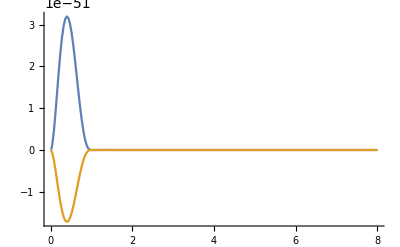

```mathematica
βmax=20;
mysubs={β->βmax,n->4/3,l->λ-1/2};
λroot=FindRoot[(1/SS1)/.{α->β*n}/.mysubs,{λ,22.5+0.01*I}]
SS1/.{α->β*n}/.{β->βmax,n->4/3,l->λ-1/2}/.λroot
deq=1/r^2*D[r^2*D[R[r],r],r]+(β^2-(λ^2-1/4)/r^2+(n^2-1)*β^2*HeavisideTheta[1-r])*R[r];
ic={R[r0]== r0^(l+1),R'[r0]==(l+1)* r0^l}/.{r0->10^(-3)}/.mysubs/.λroot
dsol=First@NDSolve[Join[ic,{deq==0}/.mysubs/.λroot],R[r],{r,10^(-3),10.0}]
Plot[{Re[R[r]]/.dsol,Im[R[r]]/.dsol},{r,0,8},PlotRange->All,PlotPoints->200]
```

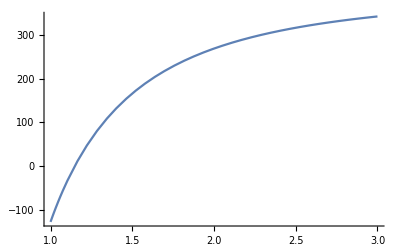

```mathematica
Plot[Re[β^2-(λ^2-1/4)/r^2+(n^2-1)*β^2*HeavisideTheta[1-r]]/.{β->βmax}/.λroot,{r,0.1,3},PlotRange->All]
```